```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π = ReadList["plot2pi.txt", {Number,Number}];
Fq3π  = ReadList["plot3pi.txt", {Number,Number}];
Fq4π  = ReadList["plot4pi.txt", {Number,Number}];
Fq5π  = ReadList["plot5pi.txt", {Number,Number}];
Fqωπ = ReadList["omega.txt", {Number,Number}];
picωπ=ListPlot[Fqωπ , Joined->True, PlotRange->All];
pic2π=ListPlot[Fq2π , Joined->True, PlotRange->All];
pic3π=ListPlot[Fq3π , Joined->True, PlotRange->All];
pic4π=ListPlot[Fq4π , Joined->True, PlotRange->All];
pic5π=ListPlot[Fq5π , Joined->True, PlotRange->All];
```

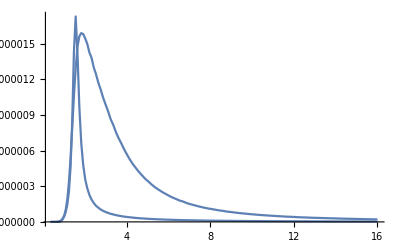

```mathematica
Show[{ListPlot[{#[[1]],4#[[2]]}&/@Fqωπ , Joined->True, PlotRange->All],pic4π},PlotRange-> All]
```

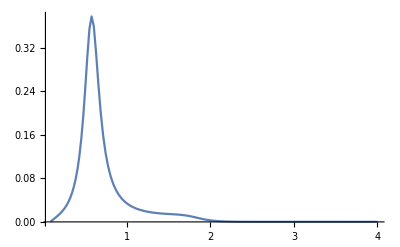

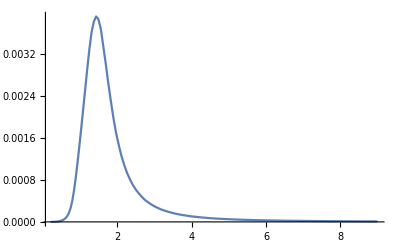

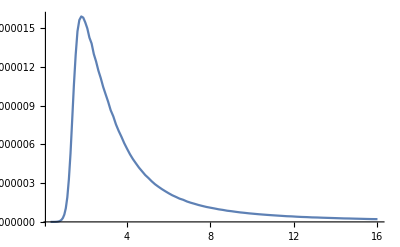

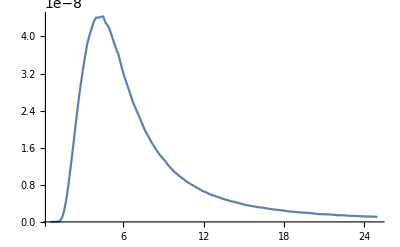

```mathematica
pic2π
pic3π
pic4π
pic5π
```

```mathematica
BWr[qsum_]:=Module[{ret,mRho,gammaRho,mRhopr,gammaRhopr,beta,m1,m2,mQ2,dRho,pPiRho,dRhopr,pPiRhopr,dQ,pPiQ,BRhoDem,BRho,BRhoprDem,BRhopr},mRho=0.775;
gammaRho=0.149;
mRhopr=1.364;
gammaRhopr=0.400;
beta=-0.108;
m1=0.13957018;m2=0.13957018;
mQ2=qsum*qsum;
dRho=mRho*mRho-m1*m1-m2*m2;
pPiRho=(1.0/mRho)*Sqrt[(dRho*dRho)/4.0-m1*m1*m2*m2];
dRhopr=mRhopr*mRhopr-m1*m1-m2*m2;
pPiRhopr=(1.0/mRhopr)*Sqrt[(dRhopr*dRhopr)/4.0-m1*m1*m2*m2];
dQ=mQ2-m1*m1-m2*m2;
pPiQ=(1.0/Sqrt[mQ2])*Sqrt[(dQ*dQ)/4.0-m1*m1*m2*m2];
gammaRho=gammaRho*mRho/Sqrt[mQ2]*Power[(pPiQ/pPiRho),3];
BRhoDem=mRho*mRho-mQ2+I*(-1.0*mRho*gammaRho);
BRho=mRho*mRho/BRhoDem;
gammaRhopr=gammaRhopr*mRhopr/Sqrt[mQ2]*Power[(pPiQ/pPiRhopr),3];
BRhoprDem=mRhopr*mRhopr-mQ2+I*(-1.0*mRho*gammaRhopr);
BRhopr=mRhopr*mRhopr/BRhoprDem;
ret=(BRho+beta*BRhopr)/(1+beta);
Return[ret]]
ret1=BWr[q]*Conjugate[BWr[q]];
mpi=0.13957018;
mπ=mpi;
ret2=ret1*(4*mpi^2-q*q);
ret3=ret2/(-3 q*q);
λr=Sqrt[(q^2-4 mpi^2)/q^2];
ret4=ret3*λr/(8 π);
ret5=ret4/.{q->Sqrt[q2]};
table=Table[{x,Interpolation[Fq2π][x]}, {x,0.0878227,2,0.0001}];
```

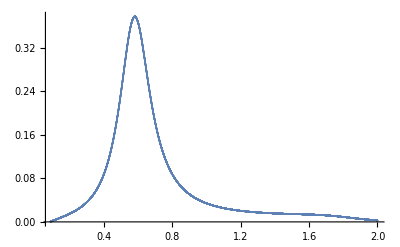

```mathematica
table2=ListPlot[table, PlotRange->All]
```

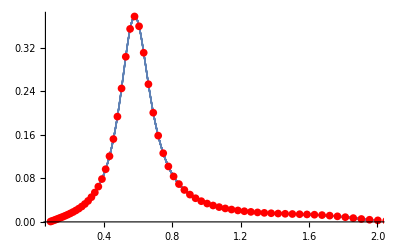

```mathematica
Show[table2, ListPlot[Fq2π, PlotRange->All,PlotStyle-> Red]]
```

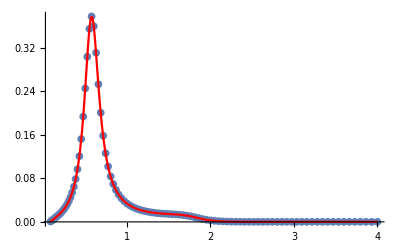

```mathematica
Show[ListPlot[Fq2π, PlotRange->All],Plot[ret5, {q2,4mpi^2,4 }, PlotRange->All, PlotStyle->Red]]
```

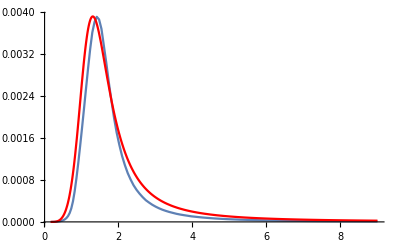

```mathematica
Show[ListPlot[b, Joined->True, PlotRange->All],Plot[Fq3π/4.4, {q2,9mpi^2,9 }, PlotRange->All, PlotStyle->Red], PlotRange-> All]
```

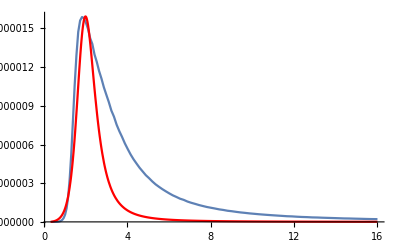

```mathematica
Show[ListPlot[c, Joined->True, PlotRange->All],Plot[Fq4π/10500, {q2,16mpi^2, 16 }, PlotRange->All, PlotStyle->Red], PlotRange-> All]
```

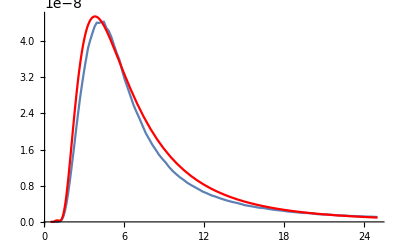

```mathematica
Show[ListPlot[d, Joined->True, PlotRange->All],Plot[Fq5π/27000, {q2,25mpi^2, 25}, PlotRange->All, PlotStyle->Red], PlotRange-> All]
```

```mathematica
Interpolation[a][4]
```

0.000105379